```mathematica
path="/run/media/vittorio/Extreme SSD/backup/Onedrive/myPHDfolder/scienza/datasets/2010-FreeEnergyMultimodeQED/plots/";
```

## Figure 1: Reduced interaction matrices (qxq)

```mathematica
Jred[p_,q_]:=Table[Cos[2 Pi p /q i j],{i,0,q-1},{j,0,q-1}]
```

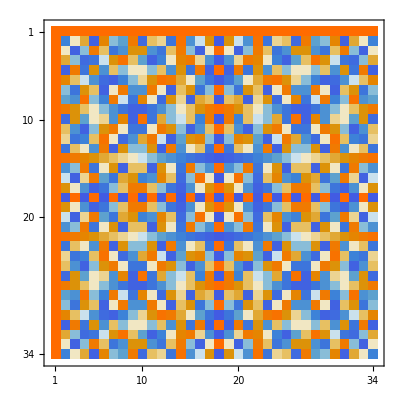

```mathematica
MatrixPlot[Jred[21,34]]
```

```mathematica
params={{8,13},{13,21},{21,34},{34,55}};
Table[
p=par[[1]];
q=par[[2]];
fig1sf11=MatrixPlot[Jred[p,q],Frame->None];
Export[path<>"FIG1_redJqxq_p"<>ToString[p]<>"_q"<>ToString[q]<>".pdf",fig1sf11, ImageResolution->300];
,{par,params}
];
```

## Figure 1: Landscapes

```mathematica
minimum[x_,y_,z_]:= ((u-x)^2+(v-y)^2-z)Exp[(-(u-x)^2-(v-y)^2)4]
l = 10;
expr=Sum[RandomReal[{-l,l}]minimum@@Append[RandomReal[{-l,l},2],RandomReal[{-l,l}]],{1000}];
landscapeRough=Quiet@Plot3D[expr,{u,-l,l},{v,-l,l},PlotRange->All, PlotStyle->White,
MeshFunctions->{#3&}, Axes-> False, Boxed-> False]
Export[path<>"FIG1_landscape_rough.png",landscapeRough]
```

-Graphics3D-

/run/media/vittorio/Extreme SSD/backup/Onedrive/myPHDfolder/scienza/datasets/2010-FreeEnergyMultimodeQED/plots/FIG1_landscape_rough.png

```mathematica
minimum[x_,y_,z_]:= ((u-x)^2+(v-y)^2-z)Exp[(-(u-x)^2-(v-y)^2)]
l = 10;
expr=Sum[RandomReal[{-l,l}]minimum@@Append[RandomReal[{-l,l},2],RandomReal[{-l,l}]],{500}];
landscapeSmooth=Quiet@Plot3D[expr,{u,-l,l},{v,-l,l},PlotRange->All, PlotStyle->White,
MeshFunctions->{#3&}, Axes-> False, Boxed-> False]
Export[path<>"FIG1_landscape_smooth.png",landscapeSmooth]
```

-Graphics3D-

/run/media/vittorio/Extreme SSD/backup/Onedrive/myPHDfolder/scienza/datasets/2010-FreeEnergyMultimodeQED/plots/FIG1_landscape_smooth.png

## Figure 3: Basins

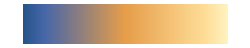

```mathematica
ColorData["M10DefaultDensityGradient","Panel"][[1]]
```

```mathematica
f[x_,y_]:=(1-y^2) (1/10(10x)^4-8(10x)^2) + (y^2)((10x)-1)^2
```

```mathematica
grad[x_,y_]:={D[f[x,y],x],D[f[x,y],y]}
```

```mathematica
solve[x0_,y0_]:=NDSolve[{x'[t]==- grad[x[t],y[t]][[1]],y'[t]==- grad[x[t],y[t]][[2]], x[0]==x0,y[0]==y0},{x,y},{t,20}]
```

```mathematica
ps={{1,1},{0.5,0.7},{8,0.9}};
n=30;
ps={RandomReal[{-1,1},n],RandomReal[{-1,1},n]}//Transpose;
surface=Show[Join[
{Plot3D[f[x,y]+2,{x,-1,1},{y,-1,1}, Lighting->{{"Ambient",White}},PlotStyle->White,
MeshFunctions->{#3&}, Axes-> False, PlotPoints->100, Boxed-> False]},
Table[
s=Check[solve@@p,-1];
If[NumericQ[s],Nothing,
Flatten@{(*ListPointPlot3D[{Join[p,{f[p[[1]],p[[2]]]+15}]},PlotStyle->Black],*)
ParametricPlot3D[Evaluate[{x[t],y[t],f[x[t],y[t]]+5}/.s[[1]]],{t,0,0.5}, PlotStyle->{Black, Thickness[0.005]}]
}]
 ,{p,ps}
]
],ImageSize->Large]
```

-Graphics3D-

```mathematica
Export[path<>"FIG3_basins.png",surface]
```

/run/media/vittorio/Extreme SSD/backup/Onedrive/myPHDfolder/scienza/datasets/2010-FreeEnergyMultimodeQED/plots/FIG3_basins.png